x Meters / G/c^2= y Mass
x Meters / (G mass)/c^2= y r_s

```mathematica
G=6.67408×10^-11
c=299792458
AU=149597870000
```

6.67408×10^-11

299792458

149597870000

```mathematica
rs/(G/c^2)
```

3.978×10^30

```mathematica
mass=1.989*10^30
radius=696340000
rs:=(2G mass)/c^2
b=radius
```

1.989×10^30

696340000

696340000

```mathematica
V[u_]:=u^2-2 u^3
```

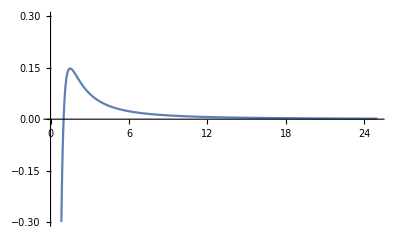

```mathematica
Veff=Plot[V[1/r],{r,0,25},PlotRange->0.3]
```

```mathematica
energy:=Plot[1/b^2,{r,0,25}]
```

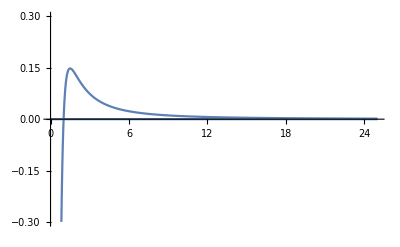

```mathematica
Show[Veff,energy]
```

```mathematica
max=1/3
```

1/3

```mathematica
Vmax=V[max]
```

2/27

```mathematica
theta[r0_,r1_]:=NIntegrate[1/(r^2 √(1/b^2-(1-rs/r)1/r^2)),{r,r0,r1}]
```

```mathematica
delphi=theta[AU,b]
```

-1.56409

```mathematica
u1=AU
u2=b
```

149597870000

696340000

```mathematica
n[z_]:=IntegerPart[z]
```

```mathematica
zf[z_]:=FractionalPart[z]
```

```mathematica
r[z_]:=u1-z*(u1-u2)
```

```mathematica
phia[z_]:= theta[AU,zf[z](AU-b)+b]
```

```mathematica
accphi[z_]:=theta[u1,u1-z(u1-u2)]
```

```mathematica
x[z_]:=Cos[accphi[z]]r[z]
y[z_]:=Sin[accphi[z]]r[z]
```

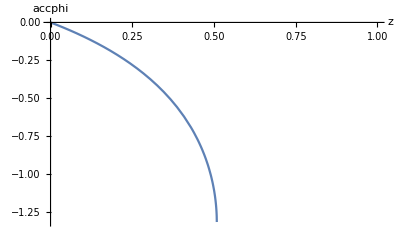

```mathematica
Plot[accphi[z],{z,0,1},AxesLabel->{"z", "accphi"}]
```

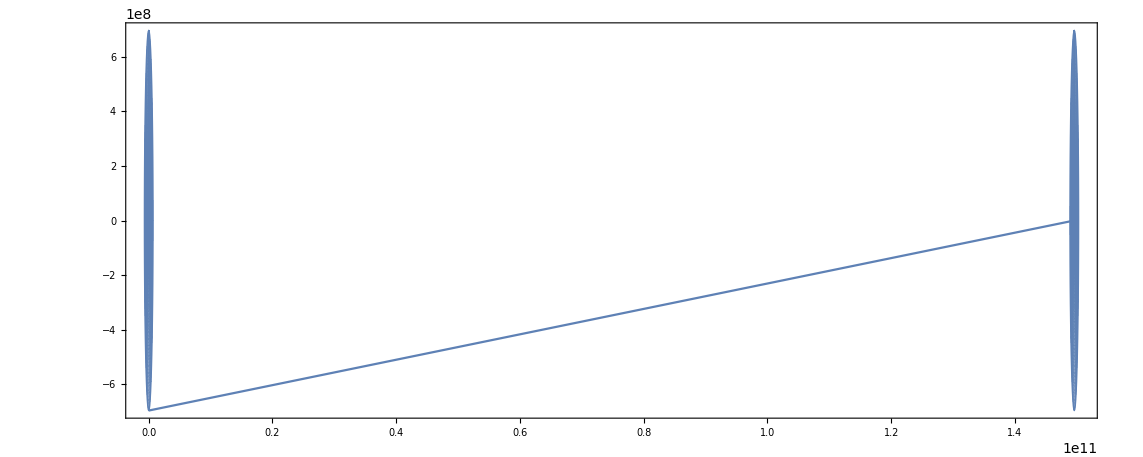

```mathematica
sun=ParametricPlot[{r Sin[k],r Cos[k]},{k,0,2π},{r,0,radius},Mesh->False];
earth=ParametricPlot[{AU+r Sin[k],r Cos[k]},{k,0,2π},{r,0,radius},Mesh->False];
graph=ParametricPlot[{x[t],y[t]},{t,0,1},AxesLabel->{"x","y"}];
Show[sun,earth,graph,PlotRange->All]
```

```mathematica
u1=1.1rs
u2=20rs
```

3249.43

59080.6

```mathematica
b=1.3rs
```

3840.24

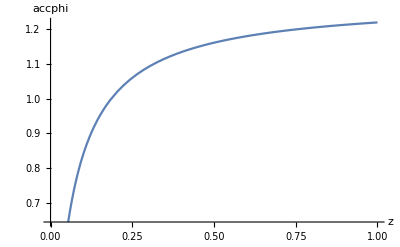

```mathematica
Plot[accphi[z],{z,0,1},AxesLabel->{"z", "accphi"}]
```

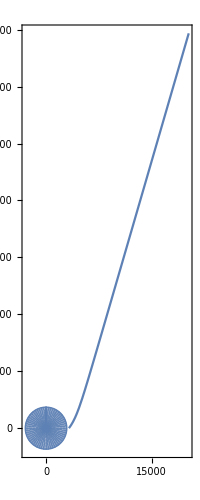

```mathematica
sun=ParametricPlot[{r Sin[k],r Cos[k]},{k,0,2π},{r,0,rs},Mesh->False];
graph=ParametricPlot[{x[t],y[t]},{t,0,1},AxesLabel->{"x","y"}];
Show[sun,graph,PlotRange->All]
```

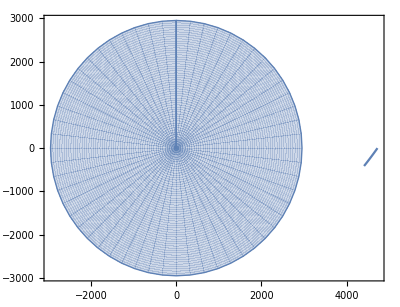

```mathematica
Cos[accphi[0.1]]/Degree
```

57.2936

```mathematica
theta[u1,u2]
```

-0.0935368

```mathematica
accphi[0.1]
```

-0.00880307

```mathematica
Solve[b==r3 √(r3/(r3-rs)),r3]
```

{{r3→2433.96-1739.28 ⅈ},{r3→2433.96+1739.28 ⅈ}}

```mathematica
fb[theta_,r_,rs_]:=(r Sin[theta])/(√(1-rs/r))
```

2954.03

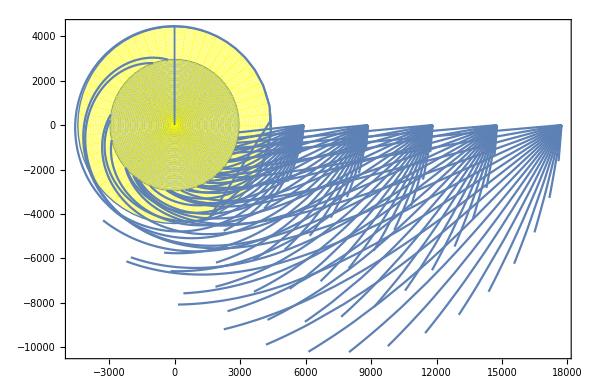

```mathematica
rs
sun=ParametricPlot[{r Sin[k],r Cos[k]},{k,0,2π},{r,0,rs},Mesh->False];
sphere=ParametricPlot[{r Sin[k],r Cos[k]},{k,0,2π},{r,0,1.5rs},PlotStyle->Yellow];
plotlist={};
For[j=2,j≤6,j++,
u1=j rs;
For[i=1,i<20,i++,
b=fb[i/40 Pi,u1,rs];
r3=Last@@Last@@Solve[b==r √(r/(r-rs)),r];
If[Element[r3,Reals]===True,u2=r3,u2=rs];
graph=ParametricPlot[{x[t],y[t]},{t,0,1},AxesLabel->{"x","y"}];
AppendTo[plotlist,graph];
]
]
Show[sun,sphere,plotlist,PlotRange->All]
```

```mathematica
rs
```

2954.03

```mathematica
u1
```

3249.43

```mathematica
b
```

590.806

```mathematica
soln=Solve[b==r √(r/(r-rs)),r]
```

{{r→562.495-774.693 ⅈ},{r→562.495+774.693 ⅈ}}

```mathematica
b
```

590.806

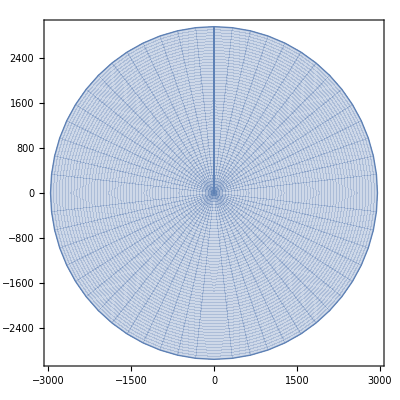

```mathematica
Show[sun]
```

```mathematica
Table[
```

2954.03

11816.1

9647.82

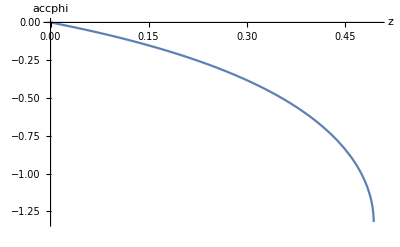

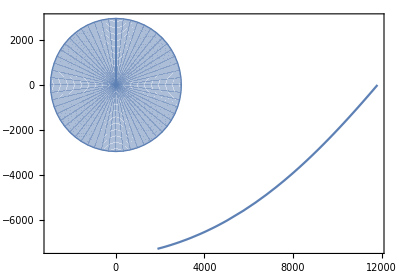

```mathematica
rs
u1=4rs
sun=ParametricPlot[{r Sin[k],r Cos[k]},{k,0,2π},{r,0,rs},Mesh->False];

b=fb[3/12 Pi,u1,rs];
Print[b];
Plot[accphi[z],{z,0,0.5},AxesLabel->{"z", "accphi"}]
r3=Last@@Last@@Solve[b==r √(r/(r-rs)),r];
If[Element[r3,Reals]===True,u2=r3,u2=rs];
graph=ParametricPlot[{x[t],y[t]},{t,0,1},AxesLabel->{"x","y"}];
Show[sun,graph,PlotRange->All]
```

```mathematica
N[(3 √3)/2]
```

2.59808

```mathematica
Solve[
```

```mathematica
fb[i,u1,rs]
```

```mathematica
fb[1/10 Pi,10rs,rs]
```

9622.23

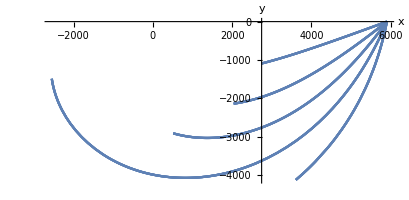

```mathematica
Show[plotlist,PlotRange->All]
```

```mathematica
wtf=Last@@Last@@Solve[b==r √(r/(r-rs)),r]
```

4431.04

2954.03

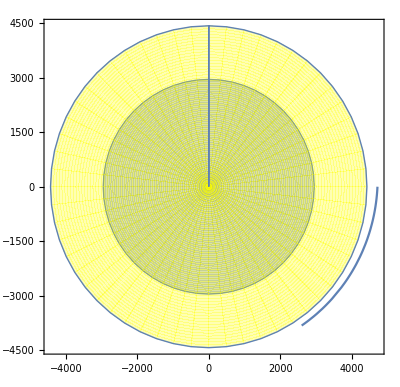

```mathematica
rs
sun=ParametricPlot[{r Sin[k],r Cos[k]},{k,0,2π},{r,0,rs},Mesh->False];
sphere=ParametricPlot[{r Sin[k],r Cos[k]},{k,0,2π},{r,0,1.5rs},PlotStyle->Yellow];
plotlist={};

u1=1.6rs;

b=fb[19/40 Pi,u1,rs];
r3=Last@@Last@@Solve[b==r √(r/(r-rs)),r];
If[Element[r3,Reals]===True,u2=r3,u2=rs];
graph=ParametricPlot[{x[t],y[t]},{t,0,1},AxesLabel->{"x","y"}];
AppendTo[plotlist,graph];


Show[sun,sphere,plotlist,PlotRange->All]
```

```mathematica
fb[9/20 Pi,u1,rs]
```

7623.23

```mathematica
(3 √3)/2 rs
```

7674.79

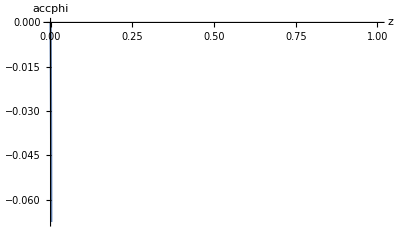

```mathematica
Plot[accphi[z],{z,0,1},AxesLabel->{"z", "accphi"}]
```